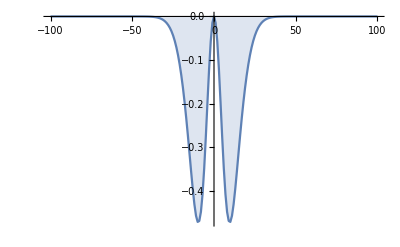

-Graphics-

```mathematica
Subscript[σ, A]=5;Subscript[σ, B]=10; A=1; b=1; n=200;
f[k_]:=A(ⅇ^(-k^2/(2 Subscript[σ, A]^2))-b ⅇ^(-k^2/(2 Subscript[σ, B]^2)));
DiscretePlot[f[k],{k,-n/2,n/2},PlotRange->Full]
W=Table[f[i-j],{i,n},{j,n}] ;
ListDensityPlot[W,ColorFunction->"GrayTones",PlotLegends->Automatic]
```

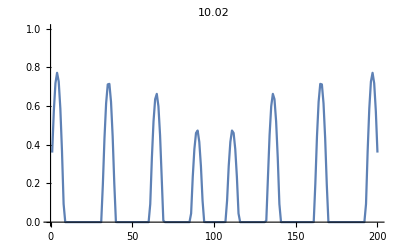

```mathematica
τ=1; T=10; dt=.03;
rect[x_]:=Max[x,0];
B[i_]:=1;

x=ConstantArray[0,n];
Monitor[
For[t=0,t<=T,t+=dt,
ẋ=1/τ(Map[rect,Table[∑_(j=1)^n W[[i,j]] *x[[j]]+B[i],{i,n}]]-x);
x+=ẋ dt;
p=ListPlot[x,PlotRange->{0,1},PlotLabel->StringForm["t = ``",t],Joined->True];
Pause[dt]
],p];
ListLinePlot[x,PlotRange->{0,1}, PlotLabel->t]
```

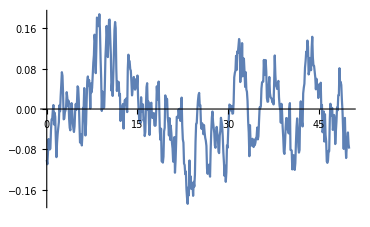

```mathematica
ListLinePlot[RandomFunction[OrnsteinUhlenbeckProcess[0,.1,1],{0,50,.1}]]
```

```mathematica
T=5;
noise=RandomFunction[OrnsteinUhlenbeckProcess[0,.03,5],{0,T,dt},n];
Monitor[
For[t=0,t<=T,t+=dt,
p=ListPlot[noise["SliceData",t],PlotLabel->"Noise",PlotRange->{-.1,.1}];
Pause[dt]
],p];
```

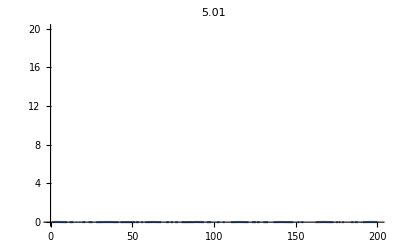

```mathematica
noise=RandomFunction[OrnsteinUhlenbeckProcess[0,.01,10],{0,T,dt},n];
x=ConstantArray[0,n];
Monitor[
For[t=0,t<=T,t+=dt,
ẋ=1/τ(Map[rect,Table[∑_(j=1)^n W[[i,j]] *x[[j]]+B[i],{i,n}]]+noise["SliceData",t]-x);
x+=ẋ dt;
p=ListPlot[x,PlotRange->{0,20},PlotLabel->StringForm["t = ``",t],Joined->True];
Pause[dt]
],p];
ListLinePlot[x,PlotRange->{0,20}, PlotLabel->t]
```